# Definitions of functions.

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Auxiliary functions

Here tensors that are used throughout the code are defined.

This command generates an array of a form {m1,n2, ... , mN,nN}.

```mathematica
dummyArray = Function[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]]}]/@Range[#]]];
```

Examples.

```mathematica
dummyArray[0]
dummyArray[1]
dummyArray[2]
dummyArray[3]
```

{}

{m1,n1}

{m1,n1,m2,n2}

{m1,n1,m2,n2,m3,n3}

This command takes a list of even number of elements, splits it in pairs, and make a metric of each pair.

```mathematica
MTDWrapper = Function[Times@@MTD@@@Partition[#,2]];
```

Examples.

```mathematica
MTDWrapper[dummyArray[1]]
MTDWrapper[dummyArray[2]]
MTDWrapper[dummyArray[3]]
```

g^m1n1

g^m1n1 g^m2n2

g^m1n1 g^m2n2 g^m3n3

This command takes two lists. The first one is the list to be symmetrized. The second one is a list of two elements. The result is a join list. Its first component it the original list; its second component is a list with the given elements begin swapped.

```mathematica
arraySymmetrization=Function[{array,argumets},Join[array,(array/.{argumets[[1]]->argumets[[2]],argumets[[2]]->argumets[[1]]})]];
```

Examples.

```mathematica
arraySymmetrization[Alphabet["Greek"],{"α","ω"}]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω,ω,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,α}

This function takes three arguments. The first one is a list, second and third are elements of the list that should be swapped. It returns a list with the elements swapped.

```mathematica
Swap=Function[#1/.{#2->#3,#3->#2}];
```

```mathematica
Alphabet["Greek"]
Swap[Alphabet["Greek"],"μ","ν"]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,ν,μ,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

This function takes an array of even number of elements and symmetrized it with respect to each index pair.

```mathematica
SymmetrizeIndexPairs= Function[indexArray,If[Length[indexArray]≠0,Partition[Fold[Join[#1,Swap[#1,#2[[1]],#2[[2]]]]&][indexArray,Partition[indexArray,2]],Length[indexArray]],{{}}] ];
```

```mathematica
SymmetrizeIndexPairs[dummyArray[0]]
SymmetrizeIndexPairs[dummyArray[1]]
SymmetrizeIndexPairs[dummyArray[2]]
SymmetrizeIndexPairs[dummyArray[3]]
```

{{}}

(m1 | n1
n1 | m1)

(m1 | n1 | m2 | n2
n1 | m1 | m2 | n2
m1 | n1 | n2 | m2
n1 | m1 | n2 | m2)

(m1 | n1 | m2 | n2 | m3 | n3
n1 | m1 | m2 | n2 | m3 | n3
m1 | n1 | n2 | m2 | m3 | n3
n1 | m1 | n2 | m2 | m3 | n3
m1 | n1 | m2 | n2 | n3 | m3
n1 | m1 | m2 | n2 | n3 | m3
m1 | n1 | n2 | m2 | n3 | m3
n1 | m1 | n2 | m2 | n3 | m3)

## I tensor

Here the definition of the I tensor is given. The tensor is responsible for the perturbative structure of g^μν.

This cell provides the definition of the I tensor with index symmetries.

```mathematica
ITensor=Function[Total[1/Power[2,Length[#]/2] MTDWrapper[RotateLeft[#,1]]&/@SymmetrizeIndexPairs[#]]];
```

Examples.

```mathematica
ITensor[{}]
ITensor[{μ,ν}]
ITensor[{μ,ν,α,β}]
ITensor[{μ,ν,α,β,ρ,σ}]
```

1

g^μν

1/2 g^αν g^βμ+1/2 g^αμ g^βν

1/8 g^ασ g^βν g^μρ+1/8 g^αν g^βσ g^μρ+1/8 g^αρ g^βν g^μσ+1/8 g^αν g^βρ g^μσ+1/8 g^ασ g^βμ g^νρ+1/8 g^αμ g^βσ g^νρ+1/8 g^αρ g^βμ g^νσ+1/8 g^αμ g^βρ g^νσ

## C tensor

Here the definition of the C tensor is given. The tensor is responsible for the perturbative structure of √-g.

This cell generates a distribution of index pairs within a single term of the C tensor.

```mathematica
CTensorIndexDistrubution =Function[{n,m},Select[Tuples[Range[n],m],Total[#]==n&]];
```

This cell evaluates a single term with a m I tensors of the C tensor. N.B. The definition of the I tensor without any index symmetries is used!

```mathematica
CTensorTerm=Function[{indexArray,m},Total[((1/(Times@@#)Times@@(ITensor/@FoldPairList[TakeDrop,indexArray,2#])))&/@CTensorIndexDistrubution[Length[indexArray]/2,m]]];
```

This cell evaluates the C tensor definition without index symmetry.

```mathematica
CTensorCore =Function[indexArray,(Power[-1,Length[indexArray]/2+#]/(Factorial[#]Power[2,#])CTensorTerm[indexArray,#]&)/@Range[Length[indexArray]/2]//Total//Expand];
```

This cell generates an array of indices with all required symmetries.

```mathematica
CTensorIndex=Function[indexArray,Partition[Flatten[Permutations[Partition[indexArray,2]]],Length[indexArray]]  ];
```

This cell defined the C tensor with index symmetries.

```mathematica
CTensor =Function[indexArray,If[Length[indexArray]≠0,Total[Expand[1/Factorial[Length[indexArray]/2] CTensorCore[#]]&/@CTensorIndex[indexArray]],1] ];
```

The next cell defined the C tensor with index symmetries.
The definition if optimized for performance, so it has a non-human-readable form.
This definition is used further.

Examples.

```mathematica
CTensor[{}]
CTensor[{μ,ν}]
CTensor[{μ,ν,α,β}]
CTensor[{μ,ν,α,β,ρ,σ}]
```

1

g^μν/2

-1/8 g^αν g^βμ-1/8 g^αμ g^βν+1/8 g^αβ g^μν

-1/48 g^ασ g^βρ g^μν-1/48 g^αρ g^βσ g^μν+1/48 g^αβ g^μν g^ρσ+1/48 g^ασ g^βν g^μρ+1/48 g^αν g^βσ g^μρ+1/48 g^αρ g^βν g^μσ+1/48 g^αν g^βρ g^μσ+1/48 g^ασ g^βμ g^νρ+1/48 g^αμ g^βσ g^νρ-1/48 g^αβ g^μσ g^νρ+1/48 g^αρ g^βμ g^νσ+1/48 g^αμ g^βρ g^νσ-1/48 g^αβ g^μρ g^νσ-1/48 g^αν g^βμ g^ρσ-1/48 g^αμ g^βν g^ρσ

## CIII tensor

Here the definition of the C tensor is given. The tensor is responsible for the perturbative structure of √-g g^μν g^αβ g^ρσ.
Indices μ,ν,α,β,ρ,σ are called external. Indices contracted with the small metric perturbations are called internal.

This cell generates an array of distributed internal indices.

```mathematica
CIIITensorInternalIndices=Function[indexArray , Function[FoldPairList[TakeDrop,indexArray,2#]]/@(Function[n,Select[Tuples[Range[0,n],4],Total[#]==n&]])[Length[indexArray]/2] ];
```

This cell generates an array of disturbed internal and external indices.

```mathematica
CIIITensorIndices=Function[{indexArrayExternal,indexArrayInternal},  Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CIIITensorInternalIndices[indexArrayInternal]  ];
```

This cell defines the CIII tensor with the symmetry with respect to index pairs.

```mathematica
CIIITensorCore =Function[ {indexArrayExternal,indexArrayInternal},Total[  Function[(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[#[[1]]]/2)CTensor[#[[1]]](Times@@ITensor/@#[[2;;]]) ]/@CIIITensorIndices[indexArrayExternal,indexArrayInternal]  ]  ];
```

This cell defined the CIII tensor with symmetries.

```mathematica
CIIITensor=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CIIITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]  ];
```

Examples

```mathematica
CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[0]]
CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[1]]
CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[2]]
```

g^αβ g^μν g^ρσ

-1/2 g^αβ g^μν g^m1σ g^n1ρ-1/2 g^αβ g^μν g^m1ρ g^n1σ-1/2 g^μν g^m1β g^n1α g^ρσ-1/2 g^μν g^m1α g^n1β g^ρσ+1/2 g^αβ g^μν g^m1n1 g^ρσ-1/2 g^αβ g^m1ν g^n1μ g^ρσ-1/2 g^αβ g^m1μ g^n1ν g^ρσ

1/8 g^m1σ g^m2ν g^n1ρ g^n2μ g^αβ+1/8 g^m1ρ g^m2ν g^n1σ g^n2μ g^αβ+1/8 g^m1σ g^m2μ g^n1ρ g^n2ν g^αβ+1/8 g^m1ρ g^m2μ g^n1σ g^n2ν g^αβ+1/8 g^m1ν g^m2σ g^n1μ g^n2ρ g^αβ+1/8 g^m1μ g^m2σ g^n1ν g^n2ρ g^αβ+1/8 g^m1ν g^m2ρ g^n1μ g^n2σ g^αβ+1/8 g^m1μ g^m2ρ g^n1ν g^n2σ g^αβ+1/8 g^m1σ g^m2ρ g^n1n2 g^μν g^αβ+1/8 g^m1ρ g^m2σ g^n1n2 g^μν g^αβ-1/8 g^m1σ g^m2n2 g^n1ρ g^μν g^αβ+1/8 g^m1n2 g^m2σ g^n1ρ g^μν g^αβ-1/8 g^m1ρ g^m2n2 g^n1σ g^μν g^αβ+1/8 g^m1n2 g^m2ρ g^n1σ g^μν g^αβ+1/8 g^m1σ g^m2n1 g^n2ρ g^μν g^αβ-1/8 g^m1n1 g^m2σ g^n2ρ g^μν g^αβ+1/8 g^m1m2 g^n1σ g^n2ρ g^μν g^αβ+1/8 g^m1ρ g^m2n1 g^n2σ g^μν g^αβ-1/8 g^m1n1 g^m2ρ g^n2σ g^μν g^αβ+1/8 g^m1m2 g^n1ρ g^n2σ g^μν g^αβ+1/8 g^m1ν g^m2μ g^n1n2 g^ρσ g^αβ+1/8 g^m1μ g^m2ν g^n1n2 g^ρσ g^αβ-1/8 g^m1ν g^m2n2 g^n1μ g^ρσ g^αβ+1/8 g^m1n2 g^m2ν g^n1μ g^ρσ g^αβ-1/8 g^m1μ g^m2n2 g^n1ν g^ρσ g^αβ+1/8 g^m1n2 g^m2μ g^n1ν g^ρσ g^αβ+1/8 g^m1ν g^m2n1 g^n2μ g^ρσ g^αβ-1/8 g^m1n1 g^m2ν g^n2μ g^ρσ g^αβ+1/8 g^m1m2 g^n1ν g^n2μ g^ρσ g^αβ+1/8 g^m1μ g^m2n1 g^n2ν g^ρσ g^αβ-1/8 g^m1n1 g^m2μ g^n2ν g^ρσ g^αβ+1/8 g^m1m2 g^n1μ g^n2ν g^ρσ g^αβ-1/8 g^m1n2 g^m2n1 g^μν g^ρσ g^αβ+1/8 g^m1n1 g^m2n2 g^μν g^ρσ g^αβ-1/8 g^m1m2 g^n1n2 g^μν g^ρσ g^αβ+1/8 g^m1σ g^m2β g^n1ρ g^n2α g^μν+1/8 g^m1ρ g^m2β g^n1σ g^n2α g^μν+1/8 g^m1σ g^m2α g^n1ρ g^n2β g^μν+1/8 g^m1ρ g^m2α g^n1σ g^n2β g^μν+1/8 g^m1β g^m2σ g^n1α g^n2ρ g^μν+1/8 g^m1α g^m2σ g^n1β g^n2ρ g^μν+1/8 g^m1β g^m2ρ g^n1α g^n2σ g^μν+1/8 g^m1α g^m2ρ g^n1β g^n2σ g^μν+1/8 g^m1ν g^m2β g^n1μ g^n2α g^ρσ+1/8 g^m1μ g^m2β g^n1ν g^n2α g^ρσ+1/8 g^m1ν g^m2α g^n1μ g^n2β g^ρσ+1/8 g^m1μ g^m2α g^n1ν g^n2β g^ρσ+1/8 g^m1β g^m2ν g^n1α g^n2μ g^ρσ+1/8 g^m1α g^m2ν g^n1β g^n2μ g^ρσ+1/8 g^m1β g^m2μ g^n1α g^n2ν g^ρσ+1/8 g^m1α g^m2μ g^n1β g^n2ν g^ρσ+1/8 g^m1β g^m2α g^n1n2 g^μν g^ρσ+1/8 g^m1α g^m2β g^n1n2 g^μν g^ρσ-1/8 g^m1β g^m2n2 g^n1α g^μν g^ρσ+1/8 g^m1n2 g^m2β g^n1α g^μν g^ρσ-1/8 g^m1α g^m2n2 g^n1β g^μν g^ρσ+1/8 g^m1n2 g^m2α g^n1β g^μν g^ρσ+1/8 g^m1β g^m2n1 g^n2α g^μν g^ρσ-1/8 g^m1n1 g^m2β g^n2α g^μν g^ρσ+1/8 g^m1m2 g^n1β g^n2α g^μν g^ρσ+1/8 g^m1α g^m2n1 g^n2β g^μν g^ρσ-1/8 g^m1n1 g^m2α g^n2β g^μν g^ρσ+1/8 g^m1m2 g^n1α g^n2β g^μν g^ρσ

## Graviton vertex

The definition of graviton vertex.

N.B. This expression is evaluated on a call and do take quite some time to evaluate!

The cell defines the T tensor for gravity.

```mathematica
TTensorGravity={μ,ν,α,β,ρ,σ,ρ1,σ1,p1,ρ2,σ2,p2}↦-FVD[p1,μ]FVD[p2,ν]MTD[α,ρ1]MTD[β,σ1]MTD[ρ,ρ2]MTD[σ,σ2]+FVD[p1,μ]FVD[p2,ν]MTD[α,ρ1]MTD[ρ,σ1]MTD[β,ρ2]MTD[σ,σ2]-2 FVD[p1,μ]FVD[p2,α]MTD[β,ρ1]MTD[ρ,σ1]MTD[ν,ρ2]MTD[σ,σ2]+2FVD[p1,μ]FVD[p2,β]MTD[ν,ρ1]MTD[α,σ1]MTD[ρ,ρ2]MTD[σ,σ2];
```

The cell defines the expression for the graviton vertex without any symmetry.

```mathematica
GravitonVertexCore = indexArray↦(TTensorGravity@@Join[{𝓂1,𝓃1,𝓂2,𝓃2,𝓂3,𝓃3},indexArray[[;;6]]])CIIITensor[{𝓂1,𝓃1,𝓂2,𝓃2,𝓂3,𝓃3},Flatten[(#[[;;2]]&)/@Partition[indexArray[[7;;]],3]]];
```

These cells define the array of input data completely symmetric in indices and momenta.

```mathematica
GravitonVertexIndexSymmetrizationMomenta=indexArray↦(Partition[Flatten[Permutations[Partition[indexArray,3]]],Length[indexArray]]);
GravitonVertexIndexSymmetrization = indexArray ↦Partition[Flatten[GravitonVertexIndexSymmetrizationMomenta/@Partition[Fold[arraySymmetrization,indexArray,(#[[;;2]]&)/@Partition[indexArray,3]],Length[indexArray]]],Length[indexArray]];
```

This cell defines the complete expression for the graviton vertex with all symmetries.

```mathematica
GravitonVertex=Function[indexArray,Contract[ⅈ(-2/κ^2)(κ)^(Length[indexArray]/3)/4 1/Power[2,Length[indexArray]/3] Total[GravitonVertexCore/@GravitonVertexIndexSymmetrization[indexArray]]]];
```

Examples

```mathematica
GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3}]
```

1/4 ⅈ κ p2^μ1 p1^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p3^μ1 p1^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p3^μ1 p2^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p1^μ1 p3^μ2 g^μ3ν3 g^ν1ν2+1/4 ⅈ κ p2^μ1 p3^μ2 g^μ3ν3 g^ν1ν2-1/4 ⅈ κ p2^μ1 g^μ2ν3 p1^μ3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2ν3 p1^μ3 g^ν1ν2-1/4 ⅈ κ g^μ1ν3 p3^μ2 p1^μ3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2ν3 p2^μ3 g^ν1ν2-1/4 ⅈ κ g^μ1ν3 p1^μ2 p2^μ3 g^ν1ν2-1/4 ⅈ κ g^μ1ν3 p3^μ2 p2^μ3 g^ν1ν2-1/4 ⅈ κ p2^μ1 g^μ2μ3 p1^ν3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2μ3 p1^ν3 g^ν1ν2-1/4 ⅈ κ g^μ1μ3 p3^μ2 p1^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p2^μ3 p1^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p3^μ3 p1^ν3 g^ν1ν2-1/4 ⅈ κ p3^μ1 g^μ2μ3 p2^ν3 g^ν1ν2-1/4 ⅈ κ g^μ1μ3 p1^μ2 p2^ν3 g^ν1ν2-1/4 ⅈ κ g^μ1μ3 p3^μ2 p2^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p1^μ3 p2^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p3^μ3 p2^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p1^μ3 p3^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1μ2 p2^μ3 p3^ν3 g^ν1ν2+1/4 ⅈ κ g^μ1ν3 g^μ2μ3 (p1·p2) g^ν1ν2+1/4 ⅈ κ g^μ1μ3 g^μ2ν3 (p1·p2) g^ν1ν2-1/4 ⅈ κ g^μ1μ2 g^μ3ν3 (p1·p2) g^ν1ν2+1/4 ⅈ κ g^μ1ν3 g^μ2μ3 (p1·p3) g^ν1ν2+1/4 ⅈ κ g^μ1μ3 g^μ2ν3 (p1·p3) g^ν1ν2-1/2 ⅈ κ g^μ1μ2 g^μ3ν3 (p1·p3) g^ν1ν2+1/4 ⅈ κ g^μ1ν3 g^μ2μ3 (p2·p3) g^ν1ν2+1/4 ⅈ κ g^μ1μ3 g^μ2ν3 (p2·p3) g^ν1ν2-1/2 ⅈ κ g^μ1μ2 g^μ3ν3 (p2·p3) g^ν1ν2-1/4 ⅈ κ p2^μ1 p1^μ2 g^μ3ν2 g^ν1ν3-1/4 ⅈ κ p3^μ1 p1^μ2 g^μ3ν2 g^ν1ν3-1/4 ⅈ κ p2^μ1 p3^μ2 g^μ3ν2 g^ν1ν3+1/4 ⅈ κ p2^μ1 g^μ2ν2 p1^μ3 g^ν1ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 p1^μ3 g^ν1ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 p1^μ3 g^ν1ν3+1/4 ⅈ κ p1^μ1 g^μ2ν2 p2^μ3 g^ν1ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 p2^μ3 g^ν1ν3-1/4 ⅈ κ g^μ1ν2 p1^μ2 p2^μ3 g^ν1ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 p2^μ3 g^ν1ν3+1/4 ⅈ κ p2^μ1 g^μ2ν2 p3^μ3 g^ν1ν3+1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν2 p1^ν1+1/4 ⅈ κ p3^μ1 g^μ2ν3 g^μ3ν2 p1^ν1-1/4 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν3 p1^ν1-1/4 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν3 p1^ν1+1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν3 p1^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p2^μ3 p1^ν1+1/4 ⅈ κ p1^μ1 g^μ2ν3 g^μ3ν2 p2^ν1+1/4 ⅈ κ p3^μ1 g^μ2ν3 g^μ3ν2 p2^ν1-1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν2 p2^ν1-1/4 ⅈ κ g^μ1ν3 p3^μ2 g^μ3ν2 p2^ν1-1/4 ⅈ κ p1^μ1 g^μ2ν2 g^μ3ν3 p2^ν1-1/2 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν3 p2^ν1+1/4 ⅈ κ g^μ1ν2 p1^μ2 g^μ3ν3 p2^ν1+1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν3 p2^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p1^μ3 p2^ν1-1/4 ⅈ κ g^μ1ν2 g^μ2ν3 p1^μ3 p2^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p3^μ3 p2^ν1+1/4 ⅈ κ p1^μ1 g^μ2ν3 g^μ3ν2 p3^ν1+1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν2 p3^ν1-1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν2 p3^ν1-1/4 ⅈ κ p1^μ1 g^μ2ν2 g^μ3ν3 p3^ν1-1/2 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν3 p3^ν1+1/4 ⅈ κ g^μ1ν2 p1^μ2 g^μ3ν3 p3^ν1+1/4 ⅈ κ g^μ1ν2 p2^μ2 g^μ3ν3 p3^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p1^μ3 p3^ν1-1/4 ⅈ κ g^μ1ν2 g^μ2ν3 p1^μ3 p3^ν1+1/4 ⅈ κ g^μ1ν3 g^μ2ν2 p2^μ3 p3^ν1-1/4 ⅈ κ g^μ1ν2 g^μ2ν3 p2^μ3 p3^ν1-1/4 ⅈ κ p2^μ1 p1^μ2 g^μ3ν1 g^ν2ν3-1/4 ⅈ κ p3^μ1 p1^μ2 g^μ3ν1 g^ν2ν3-1/4 ⅈ κ p2^μ1 p3^μ2 g^μ3ν1 g^ν2ν3-1/4 ⅈ κ p2^μ1 g^μ2ν1 p1^μ3 g^ν2ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 p1^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p2^μ2 p1^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 p1^μ3 g^ν2ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 p2^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 p2^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 p2^μ3 g^ν2ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 p3^μ3 g^ν2ν3+1/4 ⅈ κ p2^μ1 g^μ2μ3 p1^ν1 g^ν2ν3+1/4 ⅈ κ p3^μ1 g^μ2μ3 p1^ν1 g^ν2ν3+1/4 ⅈ κ p1^μ1 g^μ2μ3 p2^ν1 g^ν2ν3+1/4 ⅈ κ p3^μ1 g^μ2μ3 p2^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ3 p1^μ2 p2^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ3 p3^μ2 p2^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ2 p1^μ3 p2^ν1 g^ν2ν3+1/4 ⅈ κ p1^μ1 g^μ2μ3 p3^ν1 g^ν2ν3+1/4 ⅈ κ p2^μ1 g^μ2μ3 p3^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ3 p1^μ2 p3^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ2 p1^μ3 p3^ν1 g^ν2ν3-1/4 ⅈ κ g^μ1μ2 p2^μ3 p3^ν1 g^ν2ν3-1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν1 p1^ν2-1/4 ⅈ κ p3^μ1 g^μ2ν3 g^μ3ν1 p1^ν2+1/4 ⅈ κ g^μ1ν3 p2^μ2 g^μ3ν1 p1^ν2+1/4 ⅈ κ g^μ1ν3 p3^μ2 g^μ3ν1 p1^ν2+1/4 ⅈ κ p2^μ1 g^μ2ν1 g^μ3ν3 p1^ν2+1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν3 p1^ν2-1/4 ⅈ κ g^μ1ν1 p2^μ2 g^μ3ν3 p1^ν2-1/2 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν3 p1^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2ν1 p2^μ3 p1^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p2^μ3 p1^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p3^μ3 p1^ν2-1/4 ⅈ κ p2^μ1 g^μ2μ3 g^ν1ν3 p1^ν2-1/4 ⅈ κ p3^μ1 g^μ2μ3 g^ν1ν3 p1^ν2+1/4 ⅈ κ g^μ1μ3 p2^μ2 g^ν1ν3 p1^ν2+1/4 ⅈ κ g^μ1μ3 p3^μ2 g^ν1ν3 p1^ν2-1/4 ⅈ κ g^μ1μ2 p2^μ3 g^ν1ν3 p1^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2μ3 p2^ν1 p1^ν2-1/4 ⅈ κ g^μ1μ3 g^μ2ν3 p2^ν1 p1^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p2^ν1 p1^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2μ3 p3^ν1 p1^ν2-1/4 ⅈ κ g^μ1μ3 g^μ2ν3 p3^ν1 p1^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p3^ν1 p1^ν2+1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν1 p2^ν2+1/4 ⅈ κ g^μ1ν3 p3^μ2 g^μ3ν1 p2^ν2+1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν3 p2^ν2-1/4 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν3 p2^ν2-1/4 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν3 p2^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p1^μ3 p2^ν2+1/4 ⅈ κ g^μ1μ3 p1^μ2 g^ν1ν3 p2^ν2+1/4 ⅈ κ g^μ1μ3 p3^μ2 g^ν1ν3 p2^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p3^ν1 p2^ν2-1/4 ⅈ κ p2^μ1 g^μ2ν3 g^μ3ν1 p3^ν2+1/4 ⅈ κ g^μ1ν3 p1^μ2 g^μ3ν1 p3^ν2+1/4 ⅈ κ g^μ1ν3 p2^μ2 g^μ3ν1 p3^ν2+1/4 ⅈ κ p1^μ1 g^μ2ν1 g^μ3ν3 p3^ν2+1/4 ⅈ κ p2^μ1 g^μ2ν1 g^μ3ν3 p3^ν2-1/2 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν3 p3^ν2-1/4 ⅈ κ g^μ1ν1 p2^μ2 g^μ3ν3 p3^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2ν1 p1^μ3 p3^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p1^μ3 p3^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2ν1 p2^μ3 p3^ν2+1/4 ⅈ κ g^μ1ν1 g^μ2ν3 p2^μ3 p3^ν2-1/4 ⅈ κ p2^μ1 g^μ2μ3 g^ν1ν3 p3^ν2+1/4 ⅈ κ g^μ1μ3 p1^μ2 g^ν1ν3 p3^ν2+1/4 ⅈ κ g^μ1μ3 p2^μ2 g^ν1ν3 p3^ν2-1/4 ⅈ κ g^μ1μ2 p1^μ3 g^ν1ν3 p3^ν2-1/4 ⅈ κ g^μ1μ2 p2^μ3 g^ν1ν3 p3^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p1^ν1 p3^ν2-1/4 ⅈ κ g^μ1ν3 g^μ2μ3 p2^ν1 p3^ν2-1/4 ⅈ κ g^μ1μ3 g^μ2ν3 p2^ν1 p3^ν2+1/4 ⅈ κ g^μ1μ2 g^μ3ν3 p2^ν1 p3^ν2+1/4 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν1 p1^ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν1 p1^ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν1 p1^ν3-1/4 ⅈ κ p2^μ1 g^μ2ν1 g^μ3ν2 p1^ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν2 p1^ν3+1/4 ⅈ κ g^μ1ν1 p2^μ2 g^μ3ν2 p1^ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν2 p1^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p2^μ3 p1^ν3-1/2 ⅈ κ g^μ1ν1 g^μ2ν2 p2^μ3 p1^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p3^μ3 p1^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p3^μ3 p1^ν3-1/4 ⅈ κ g^μ1ν2 g^μ2μ3 p2^ν1 p1^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p2^ν1 p1^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν2 p2^ν1 p1^ν3-1/4 ⅈ κ g^μ1ν2 g^μ2μ3 p3^ν1 p1^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p3^ν1 p1^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν2 p3^ν1 p1^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p2^ν2 p1^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p3^ν2 p1^ν3-1/4 ⅈ κ g^μ1μ3 g^μ2ν1 p3^ν2 p1^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν1 p3^ν2 p1^ν3+1/4 ⅈ κ p1^μ1 g^μ2ν2 g^μ3ν1 p2^ν3+1/4 ⅈ κ p3^μ1 g^μ2ν2 g^μ3ν1 p2^ν3-1/4 ⅈ κ g^μ1ν2 p1^μ2 g^μ3ν1 p2^ν3-1/4 ⅈ κ g^μ1ν2 p3^μ2 g^μ3ν1 p2^ν3-1/4 ⅈ κ p3^μ1 g^μ2ν1 g^μ3ν2 p2^ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν2 p2^ν3+1/4 ⅈ κ g^μ1ν1 p3^μ2 g^μ3ν2 p2^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p1^μ3 p2^ν3-1/2 ⅈ κ g^μ1ν1 g^μ2ν2 p1^μ3 p2^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p3^μ3 p2^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p3^μ3 p2^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p1^ν1 p2^ν3-1/4 ⅈ κ g^μ1ν2 g^μ2μ3 p3^ν1 p2^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p3^ν1 p2^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν2 p3^ν1 p2^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p1^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ3 g^μ2ν1 p1^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν1 p1^ν2 p2^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p3^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ3 g^μ2ν1 p3^ν2 p2^ν3-1/4 ⅈ κ g^μ1μ2 g^μ3ν1 p3^ν2 p2^ν3+1/4 ⅈ κ p2^μ1 g^μ2ν2 g^μ3ν1 p3^ν3+1/4 ⅈ κ g^μ1ν1 p1^μ2 g^μ3ν2 p3^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p1^μ3 p3^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p1^μ3 p3^ν3+1/4 ⅈ κ g^μ1ν2 g^μ2ν1 p2^μ3 p3^ν3-1/4 ⅈ κ g^μ1ν1 g^μ2ν2 p2^μ3 p3^ν3+1/4 ⅈ κ g^μ1μ3 g^μ2ν2 p2^ν1 p3^ν3+1/4 ⅈ κ g^μ1ν1 g^μ2μ3 p1^ν2 p3^ν3-1/2 ⅈ κ g^μ1ν3 g^μ2ν2 g^μ3ν1 (p1·p2)+1/4 ⅈ κ g^μ1ν2 g^μ2ν3 g^μ3ν1 (p1·p2)+1/4 ⅈ κ g^μ1ν3 g^μ2ν1 g^μ3ν2 (p1·p2)-1/2 ⅈ κ g^μ1ν1 g^μ2ν3 g^μ3ν2 (p1·p2)-1/4 ⅈ κ g^μ1ν2 g^μ2ν1 g^μ3ν3 (p1·p2)+1/2 ⅈ κ g^μ1ν1 g^μ2ν2 g^μ3ν3 (p1·p2)+1/4 ⅈ κ g^μ1ν2 g^μ2μ3 g^ν1ν3 (p1·p2)-1/2 ⅈ κ g^μ1μ3 g^μ2ν2 g^ν1ν3 (p1·p2)+1/4 ⅈ κ g^μ1μ2 g^μ3ν2 g^ν1ν3 (p1·p2)-1/2 ⅈ κ g^μ1ν1 g^μ2μ3 g^ν2ν3 (p1·p2)+1/4 ⅈ κ g^μ1μ3 g^μ2ν1 g^ν2ν3 (p1·p2)+1/4 ⅈ κ g^μ1μ2 g^μ3ν1 g^ν2ν3 (p1·p2)-1/4 ⅈ κ g^μ1ν3 g^μ2ν2 g^μ3ν1 (p1·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2ν3 g^μ3ν1 (p1·p3)+1/4 ⅈ κ g^μ1ν3 g^μ2ν1 g^μ3ν2 (p1·p3)-1/2 ⅈ κ g^μ1ν1 g^μ2ν3 g^μ3ν2 (p1·p3)-1/2 ⅈ κ g^μ1ν2 g^μ2ν1 g^μ3ν3 (p1·p3)+1/2 ⅈ κ g^μ1ν1 g^μ2ν2 g^μ3ν3 (p1·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2μ3 g^ν1ν3 (p1·p3)-1/4 ⅈ κ g^μ1μ3 g^μ2ν2 g^ν1ν3 (p1·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν2 g^ν1ν3 (p1·p3)-1/2 ⅈ κ g^μ1ν1 g^μ2μ3 g^ν2ν3 (p1·p3)+1/4 ⅈ κ g^μ1μ3 g^μ2ν1 g^ν2ν3 (p1·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν1 g^ν2ν3 (p1·p3)-1/2 ⅈ κ g^μ1ν3 g^μ2ν2 g^μ3ν1 (p2·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2ν3 g^μ3ν1 (p2·p3)+1/4 ⅈ κ g^μ1ν3 g^μ2ν1 g^μ3ν2 (p2·p3)-1/4 ⅈ κ g^μ1ν1 g^μ2ν3 g^μ3ν2 (p2·p3)-1/2 ⅈ κ g^μ1ν2 g^μ2ν1 g^μ3ν3 (p2·p3)+1/2 ⅈ κ g^μ1ν1 g^μ2ν2 g^μ3ν3 (p2·p3)+1/4 ⅈ κ g^μ1ν2 g^μ2μ3 g^ν1ν3 (p2·p3)-1/2 ⅈ κ g^μ1μ3 g^μ2ν2 g^ν1ν3 (p2·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν2 g^ν1ν3 (p2·p3)-1/4 ⅈ κ g^μ1ν1 g^μ2μ3 g^ν2ν3 (p2·p3)+1/4 ⅈ κ g^μ1μ3 g^μ2ν1 g^ν2ν3 (p2·p3)+1/4 ⅈ κ g^μ1μ2 g^μ3ν1 g^ν2ν3 (p2·p3)

## CI tensor

Here the definition of the C tensor is given. The tensor is responsible for the perturbative structure of √-g g^μν.

This cell generates a distributions of internal indices.

```mathematica
CITensorInternalIndices=Function[indexArray,  FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],2],Total[#]==n&])[Length[indexArray]/2]  ];
```

This cell generates a distribution of both internal and external indices.

```mathematica
CITensorIndices=Function[{indexArrayExternal,indexArrayInternal},Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CITensorInternalIndices[indexArrayInternal]  ];
```

This cell gives the definition of the CI tensor without all symmetries.

```mathematica
CITensorCore = Function[{indexArrayExternal,indexArrayInternal},Total[  (indexArray↦(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[indexArray[[1]]]/2)CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CITensorIndices[indexArrayExternal,indexArrayInternal]  ]  ];
```

This cell gives the definition of the CI tensor with symmetries.

```mathematica
CITensor=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]  ];
```

Examples

```mathematica
CITensor[{μ,ν},{}]
CITensor[{μ,ν},{m,n}]
CITensor[{μ,ν},dummyArray[2]]
```

g^μν

-1/2 g^mν g^nμ-1/2 g^mμ g^nν+1/2 g^μν g^mn

1/8 g^m1ν g^m2μ g^n1n2+1/8 g^m1μ g^m2ν g^n1n2-1/8 g^μν g^m1m2 g^n1n2-1/8 g^m1ν g^m2n2 g^n1μ+1/8 g^m1n2 g^m2ν g^n1μ-1/8 g^m1μ g^m2n2 g^n1ν+1/8 g^m1n2 g^m2μ g^n1ν+1/8 g^m1ν g^m2n1 g^n2μ-1/8 g^m1n1 g^m2ν g^n2μ+1/8 g^m1m2 g^n1ν g^n2μ+1/8 g^m1μ g^m2n1 g^n2ν-1/8 g^m1n1 g^m2μ g^n2ν+1/8 g^m1m2 g^n1μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2

## Graviton-Scalar vertex

The definition of graviton-scalar interaction vertex for massless scalars.
TTensorGravityScalar contains information on the scalar field momenta.

```mathematica
TTensorGravityScalar={m,n,p,q}↦Expand[-1/2 1/2(FVD[p,m]FVD[q,n]+FVD[q,m]FVD[p,n])];
GravitonScalarVertex=Function[indexArray,Contract[2(ⅈ κ^((Length[indexArray]-2)/2))CITensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityScalar[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]]  ];
```

Examples

```mathematica
GravitonScalarVertex[{μ,ν,p1,p2}]
GravitonScalarVertex[{μ,ν,α,β,p,q}]
```

-1/2 ⅈ κ g^μν (p1·p2)+1/2 ⅈ κ p1^ν p2^μ+1/2 ⅈ κ p1^μ p2^ν

1/8 ⅈ κ^2 p^β q^α g^μν+1/8 ⅈ κ^2 p^α q^β g^μν-1/8 ⅈ κ^2 p^μ q^α g^βν-1/8 ⅈ κ^2 p^μ q^β g^αν-1/8 ⅈ κ^2 p^α q^μ g^βν-1/8 ⅈ κ^2 p^β q^μ g^αν-1/8 ⅈ κ^2 p^ν q^α g^βμ-1/8 ⅈ κ^2 p^ν q^β g^αμ+1/8 ⅈ κ^2 p^ν q^μ g^αβ-1/8 ⅈ κ^2 p^α q^ν g^βμ-1/8 ⅈ κ^2 p^β q^ν g^αμ+1/8 ⅈ κ^2 p^μ q^ν g^αβ+1/8 ⅈ κ^2 g^αν g^βμ (p·q)+1/8 ⅈ κ^2 g^αμ g^βν (p·q)-1/8 ⅈ κ^2 g^αβ g^μν (p·q)

## Graviton-Massive Scalar vertex

The definition of graviton-massive scalar interaction vertex for massless scalars.
TTensorGravityScalar contains information on the scalar field momenta.

```mathematica
GravitonMassiveScalarVertex=Function[{indexArray,m},Contract[2(ⅈ κ^((Length[indexArray]-2)/2))(CITensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityScalar[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]  -m^2/2 CTensor[indexArray[[;;Length[indexArray]-2]]] )]];
```

Examples

```mathematica
GravitonMassiveScalarVertex[{μ,ν,p1,p2},m]
GravitonMassiveScalarVertex[{μ,ν,α,β,p,q},m]
```

-1/2 ⅈ κ m^2 g^μν-1/2 ⅈ κ g^μν (p1·p2)+1/2 ⅈ κ p1^ν p2^μ+1/2 ⅈ κ p1^μ p2^ν

1/8 ⅈ κ^2 m^2 g^αν g^βμ+1/8 ⅈ κ^2 m^2 g^αμ g^βν-1/8 ⅈ κ^2 m^2 g^αβ g^μν+1/8 ⅈ κ^2 p^β q^α g^μν+1/8 ⅈ κ^2 p^α q^β g^μν-1/8 ⅈ κ^2 p^μ q^α g^βν-1/8 ⅈ κ^2 p^μ q^β g^αν-1/8 ⅈ κ^2 p^α q^μ g^βν-1/8 ⅈ κ^2 p^β q^μ g^αν-1/8 ⅈ κ^2 p^ν q^α g^βμ-1/8 ⅈ κ^2 p^ν q^β g^αμ+1/8 ⅈ κ^2 p^ν q^μ g^αβ-1/8 ⅈ κ^2 p^α q^ν g^βμ-1/8 ⅈ κ^2 p^β q^ν g^αμ+1/8 ⅈ κ^2 p^μ q^ν g^αβ+1/8 ⅈ κ^2 g^αν g^βμ (p·q)+1/8 ⅈ κ^2 g^αμ g^βν (p·q)-1/8 ⅈ κ^2 g^αβ g^μν (p·q)

```mathematica
GravitonScalarVertex[{μ,ν,p1,p2}]==GravitonMassiveScalarVertex[{μ,ν,p1,p2},0]
GravitonScalarVertex[{μ,ν,α,β,p,q}]==GravitonMassiveScalarVertex[{μ,ν,α,β,p,q},0]
GravitonScalarVertex[{μ,ν,α,β,ρ,σ,p,q}]==GravitonMassiveScalarVertex[{μ,ν,α,β,ρ,σ,p,q},0]
```

True

True

True

## CII tensor

CII definition.

The tensor is related with √-g g^μν g^αβ , so μ,ν,α,β indices are taken as a separate argument.

```mathematica
CIITensorInternalIndices=indexArray↦FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],3],Total[#]==n&])[Length[indexArray]/2];
CIITensorExternalIndices=indexArray↦Join[{{}},Partition[indexArray,2]];
CIITensorIndices={indexArrayExternal,indexArrayInternal}↦Function[MapThread[Join,{CIITensorExternalIndices[indexArrayExternal],#}]]/@CIITensorInternalIndices[indexArrayInternal];
CIITensorCore = {indexArrayExternal,indexArrayInternal}↦Total[  (indexArray↦(-1)^(Length[indexArrayInternal]/2)(-1)^(-Length[indexArray[[1]]]/2)CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CIITensorIndices[indexArrayExternal,indexArrayInternal]  ];
CIITensor={indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CIITensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

Examples

```mathematica
CIITensor[{μ,ν,α,β},{}]
CIITensor[dummyArray[2],{μ,ν}]
CIITensor[{μ,ν,ρ,σ},dummyArray[2]]
```

g^αβ g^μν

-1/2 g^m1ν g^m2n2 g^n1μ-1/2 g^m1μ g^m2n2 g^n1ν-1/2 g^m1n1 g^m2ν g^n2μ-1/2 g^m1n1 g^m2μ g^n2ν+1/2 g^μν g^m1n1 g^m2n2

1/8 g^m1σ g^m2ν g^n1ρ g^n2μ+1/8 g^m1ρ g^m2ν g^n1σ g^n2μ+1/8 g^m1ν g^m2n1 g^n2μ g^ρσ-1/8 g^m1n1 g^m2ν g^n2μ g^ρσ+1/8 g^m1m2 g^n1ν g^n2μ g^ρσ+1/8 g^m1σ g^m2μ g^n1ρ g^n2ν+1/8 g^m1ρ g^m2μ g^n1σ g^n2ν+1/8 g^m1ν g^m2σ g^n1μ g^n2ρ+1/8 g^m1μ g^m2σ g^n1ν g^n2ρ+1/8 g^m1ν g^m2ρ g^n1μ g^n2σ+1/8 g^m1μ g^m2ρ g^n1ν g^n2σ+1/8 g^μν g^m1σ g^m2ρ g^n1n2+1/8 g^μν g^m1ρ g^m2σ g^n1n2-1/8 g^μν g^m1σ g^m2n2 g^n1ρ+1/8 g^μν g^m1n2 g^m2σ g^n1ρ-1/8 g^μν g^m1ρ g^m2n2 g^n1σ+1/8 g^μν g^m1n2 g^m2ρ g^n1σ+1/8 g^μν g^m1σ g^m2n1 g^n2ρ-1/8 g^μν g^m1n1 g^m2σ g^n2ρ+1/8 g^μν g^m1m2 g^n1σ g^n2ρ+1/8 g^μν g^m1ρ g^m2n1 g^n2σ-1/8 g^μν g^m1n1 g^m2ρ g^n2σ+1/8 g^μν g^m1m2 g^n1ρ g^n2σ+1/8 g^m1ν g^m2μ g^n1n2 g^ρσ+1/8 g^m1μ g^m2ν g^n1n2 g^ρσ-1/8 g^m1ν g^m2n2 g^n1μ g^ρσ+1/8 g^m1n2 g^m2ν g^n1μ g^ρσ-1/8 g^m1μ g^m2n2 g^n1ν g^ρσ+1/8 g^m1n2 g^m2μ g^n1ν g^ρσ+1/8 g^m1μ g^m2n1 g^n2ν g^ρσ-1/8 g^m1n1 g^m2μ g^n2ν g^ρσ+1/8 g^m1m2 g^n1μ g^n2ν g^ρσ-1/8 g^μν g^m1n2 g^m2n1 g^ρσ+1/8 g^μν g^m1n1 g^m2n2 g^ρσ-1/8 g^μν g^m1m2 g^n1n2 g^ρσ

## Graviton-Vector vertex

Definition of graviton-vector interaction vertex for massless vectors.
TTensorGravityVector contains information of the vector momenta.

```mathematica
TTensorGravityVector = {μ,ν,α,β,ρ,σ,p,q}↦Calc[1/4 FVD[p,ℓ]FVD[q,𝓉](ITensor[{μ,ν,ρ,σ}]ITensor[{α,β,ℓ,𝓉}]+ITensor[{μ,ν,ℓ,𝓉}]ITensor[{α,β,ρ,σ}]-ITensor[{μ,ν,ρ,𝓉}]ITensor[{α,β,σ,ℓ}]-ITensor[{μ,ν,σ,ℓ}]ITensor[{α,β,ρ,𝓉}])];
GravitonVectorVertex=indexArray↦Calc[(ⅈ κ^(Length[indexArray]/2-2))2TTensorGravityVector[Sequence@@Join[{𝓂,𝓃,𝒶,𝒷},indexArray[[Length[indexArray]-3;;]]]]CIITensor[{𝓂,𝓃,𝒶,𝒷},indexArray[[;;Length[indexArray]-4]]]];
```

Examples

```mathematica
GravitonVectorVertex[{μ,ν,λ1,λ2,p1,p1}]
GravitonVectorVertex[{μ,ν,α,β,Subscript[λ, 1],Subscript[λ, 2],Subscript[k, 1],Subscript[k, 2]}]
```

-1/2 ⅈ κ p1^λ1 p1^λ2 g^μν+1/2 ⅈ κ p1^2 g^λ1λ2 g^μν+1/2 ⅈ κ p1^λ1 p1^μ g^λ2ν+1/2 ⅈ κ p1^λ2 p1^μ g^λ1ν+1/2 ⅈ κ p1^λ1 p1^ν g^λ2μ+1/2 ⅈ κ p1^λ2 p1^ν g^λ1μ-ⅈ κ p1^μ p1^ν g^λ1λ2-1/2 ⅈ κ p1^2 g^λ1ν g^λ2μ-1/2 ⅈ κ p1^2 g^λ1μ g^λ2ν

1/8 ⅈ k_2^α k_1^β g^(μ λ_2) g^(ν λ_1) κ^2+1/8 ⅈ k_1^α k_2^β g^(μ λ_2) g^(ν λ_1) κ^2-1/8 ⅈ k_1^α g^(β λ_2) k_2^μ g^(ν λ_1) κ^2-1/8 ⅈ g^(α λ_2) k_1^β k_2^μ g^(ν λ_1) κ^2+1/8 ⅈ k_2^α k_1^β g^(μ λ_1) g^(ν λ_2) κ^2+1/8 ⅈ k_1^α k_2^β g^(μ λ_1) g^(ν λ_2) κ^2-1/8 ⅈ k_2^α g^(β λ_1) k_1^μ g^(ν λ_2) κ^2-1/8 ⅈ g^(α λ_1) k_2^β k_1^μ g^(ν λ_2) κ^2-1/8 ⅈ k_2^α g^(β λ_1) g^(μ λ_2) k_1^ν κ^2-1/8 ⅈ g^(α λ_1) k_2^β g^(μ λ_2) k_1^ν κ^2+1/8 ⅈ g^(α λ_2) g^(β λ_1) k_2^μ k_1^ν κ^2+1/8 ⅈ g^(α λ_1) g^(β λ_2) k_2^μ k_1^ν κ^2-1/8 ⅈ k_1^α g^(β λ_2) g^(μ λ_1) k_2^ν κ^2-1/8 ⅈ g^(α λ_2) k_1^β g^(μ λ_1) k_2^ν κ^2+1/8 ⅈ g^(α λ_2) g^(β λ_1) k_1^μ k_2^ν κ^2+1/8 ⅈ g^(α λ_1) g^(β λ_2) k_1^μ k_2^ν κ^2-1/8 ⅈ k_2^α k_1^β g^μν g^(λ_1 λ_2) κ^2-1/8 ⅈ k_1^α k_2^β g^μν g^(λ_1 λ_2) κ^2+1/8 ⅈ k_2^α g^βν k_1^μ g^(λ_1 λ_2) κ^2+1/8 ⅈ g^αν k_2^β k_1^μ g^(λ_1 λ_2) κ^2+1/8 ⅈ k_1^α g^βν k_2^μ g^(λ_1 λ_2) κ^2+1/8 ⅈ g^αν k_1^β k_2^μ g^(λ_1 λ_2) κ^2+1/8 ⅈ k_2^α g^βμ k_1^ν g^(λ_1 λ_2) κ^2+1/8 ⅈ g^αμ k_2^β k_1^ν g^(λ_1 λ_2) κ^2-1/8 ⅈ g^αβ k_2^μ k_1^ν g^(λ_1 λ_2) κ^2+1/8 ⅈ k_1^α g^βμ k_2^ν g^(λ_1 λ_2) κ^2+1/8 ⅈ g^αμ k_1^β k_2^ν g^(λ_1 λ_2) κ^2-1/8 ⅈ g^αβ k_1^μ k_2^ν g^(λ_1 λ_2) κ^2+1/8 ⅈ k_1^α g^(β λ_2) g^μν k_2^λ_1 κ^2+1/8 ⅈ g^(α λ_2) k_1^β g^μν k_2^λ_1 κ^2-1/8 ⅈ k_1^α g^βν g^(μ λ_2) k_2^λ_1 κ^2-1/8 ⅈ g^αν k_1^β g^(μ λ_2) k_2^λ_1 κ^2-1/8 ⅈ g^(α λ_2) g^βν k_1^μ k_2^λ_1 κ^2-1/8 ⅈ g^αν g^(β λ_2) k_1^μ k_2^λ_1 κ^2-1/8 ⅈ k_1^α g^βμ g^(ν λ_2) k_2^λ_1 κ^2-1/8 ⅈ g^αμ k_1^β g^(ν λ_2) k_2^λ_1 κ^2+1/8 ⅈ g^αβ k_1^μ g^(ν λ_2) k_2^λ_1 κ^2-1/8 ⅈ g^(α λ_2) g^βμ k_1^ν k_2^λ_1 κ^2-1/8 ⅈ g^αμ g^(β λ_2) k_1^ν k_2^λ_1 κ^2+1/8 ⅈ g^αβ g^(μ λ_2) k_1^ν k_2^λ_1 κ^2+1/8 ⅈ k_2^α g^(β λ_1) g^μν k_1^λ_2 κ^2+1/8 ⅈ g^(α λ_1) k_2^β g^μν k_1^λ_2 κ^2-1/8 ⅈ k_2^α g^βν g^(μ λ_1) k_1^λ_2 κ^2-1/8 ⅈ g^αν k_2^β g^(μ λ_1) k_1^λ_2 κ^2-1/8 ⅈ g^(α λ_1) g^βν k_2^μ k_1^λ_2 κ^2-1/8 ⅈ g^αν g^(β λ_1) k_2^μ k_1^λ_2 κ^2-1/8 ⅈ k_2^α g^βμ g^(ν λ_1) k_1^λ_2 κ^2-1/8 ⅈ g^αμ k_2^β g^(ν λ_1) k_1^λ_2 κ^2+1/8 ⅈ g^αβ k_2^μ g^(ν λ_1) k_1^λ_2 κ^2-1/8 ⅈ g^(α λ_1) g^βμ k_2^ν k_1^λ_2 κ^2-1/8 ⅈ g^αμ g^(β λ_1) k_2^ν k_1^λ_2 κ^2+1/8 ⅈ g^αβ g^(μ λ_1) k_2^ν k_1^λ_2 κ^2+1/8 ⅈ g^αν g^βμ k_2^λ_1 k_1^λ_2 κ^2+1/8 ⅈ g^αμ g^βν k_2^λ_1 k_1^λ_2 κ^2-1/8 ⅈ g^αβ g^μν k_2^λ_1 k_1^λ_2 κ^2-1/8 ⅈ g^(α λ_2) g^(β λ_1) g^μν (k_1·k_2) κ^2-1/8 ⅈ g^(α λ_1) g^(β λ_2) g^μν (k_1·k_2) κ^2+1/8 ⅈ g^(α λ_2) g^βν g^(μ λ_1) (k_1·k_2) κ^2+1/8 ⅈ g^αν g^(β λ_2) g^(μ λ_1) (k_1·k_2) κ^2+1/8 ⅈ g^(α λ_1) g^βν g^(μ λ_2) (k_1·k_2) κ^2+1/8 ⅈ g^αν g^(β λ_1) g^(μ λ_2) (k_1·k_2) κ^2+1/8 ⅈ g^(α λ_2) g^βμ g^(ν λ_1) (k_1·k_2) κ^2+1/8 ⅈ g^αμ g^(β λ_2) g^(ν λ_1) (k_1·k_2) κ^2-1/8 ⅈ g^αβ g^(μ λ_2) g^(ν λ_1) (k_1·k_2) κ^2+1/8 ⅈ g^(α λ_1) g^βμ g^(ν λ_2) (k_1·k_2) κ^2+1/8 ⅈ g^αμ g^(β λ_1) g^(ν λ_2) (k_1·k_2) κ^2-1/8 ⅈ g^αβ g^(μ λ_1) g^(ν λ_2) (k_1·k_2) κ^2-1/8 ⅈ g^αν g^βμ g^(λ_1 λ_2) (k_1·k_2) κ^2-1/8 ⅈ g^αμ g^βν g^(λ_1 λ_2) (k_1·k_2) κ^2+1/8 ⅈ g^αβ g^μν g^(λ_1 λ_2) (k_1·k_2) κ^2

## E tensor

The definition of the E tensor.
𝔢_m^μ = (Σ_(n=0))^∞κ^n(-1/2
n)I_m^(μρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)... h_(ρ_n σ_n) =(Σ_(n=0))^∞κ^n E_m^(μρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n) .

```mathematica
ETensor = {indexArrayExternal,indexArrayInternal}↦Expand[Binomial[-1/2,Length[indexArrayInternal]/2]ITensor[Join[indexArrayExternal,indexArrayInternal]]];
```

Examples.

```mathematica
ETensor[{μ,ν},{}]
ETensor[{μ,ν},dummyArray[1]]
ETensor[{α,β},dummyArray[2]]
```

g^μν

-1/4 g^m1ν g^n1μ-1/4 g^m1μ g^n1ν

3/64 g^m1β g^m2α g^n1n2+3/64 g^m1α g^m2β g^n1n2+3/64 g^m1n2 g^m2β g^n1α+3/64 g^m1n2 g^m2α g^n1β+3/64 g^m1β g^m2n1 g^n2α+3/64 g^m1m2 g^n1β g^n2α+3/64 g^m1α g^m2n1 g^n2β+3/64 g^m1m2 g^n1α g^n2β

## CE tensor

The definition of C tensor.

√-g 𝔢_m^μ=(Σ_(n=0))^∞κ^n ((C_E)_m)^(μρ_1... σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n).

```mathematica
CETensorInternalIndices=indexArray↦FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],2],Total[#]==n&])[Length[indexArray]/2];
CETensorIndices={indexArrayExternal,indexArrayInternal}↦Function[MapThread[Join,{CITensorExternalIndices[indexArrayExternal],#}]]/@CITensorInternalIndices[indexArrayInternal];
CETensorCore = {indexArrayExternal,indexArrayInternal}↦Total[Function[CTensor[#[[1]]] ETensor[#[[2]][[;;2]],#[[2]][[3;;]]]  ]/@CETensorIndices[indexArrayExternal,indexArrayInternal]];
CETensor = {indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CETensorCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

Examples

```mathematica
CETensor[{μ,ν},{}]
CETensor[{μ,ν},dummyArray[1]]
CETensor[{μ,ν},dummyArray[2]]
```

g^μν

-1/4 g^m1ν g^n1μ-1/4 g^m1μ g^n1ν+1/2 g^μν g^m1n1

3/64 g^m1ν g^m2μ g^n1n2+3/64 g^m1μ g^m2ν g^n1n2-1/8 g^μν g^m1m2 g^n1n2-1/16 g^m1ν g^m2n2 g^n1μ+3/64 g^m1n2 g^m2ν g^n1μ-1/16 g^m1μ g^m2n2 g^n1ν+3/64 g^m1n2 g^m2μ g^n1ν+3/64 g^m1ν g^m2n1 g^n2μ-1/16 g^m1n1 g^m2ν g^n2μ+3/64 g^m1m2 g^n1ν g^n2μ+3/64 g^m1μ g^m2n1 g^n2ν-1/16 g^m1n1 g^m2μ g^n2ν+3/64 g^m1m2 g^n1μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2

## Graviton-Fermion vertex

The definition of graviton-fermion interaction vertex for massless Dirac fermions.
TTensorGravityDirac contains information on the scalar field momenta.

```mathematica
TTensorGravityDirac={m,n,p,q}↦Calc[1/2 GAD[m]FVD[p+q,n]];
GravitonFermionVertex=indexArray↦Calc[(ⅈ κ^((Length[indexArray]-2)/2))CETensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityDirac[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]];
```

Examples

```mathematica
GravitonFermionVertex[{μ,ν,p1,p2}]
GravitonFermionVertex[{μ,ν,α,β,p,q}]
```

1/4 ⅈ κ g^μν γ·p1+1/4 ⅈ κ g^μν γ·p2-1/8 ⅈ κ γ^ν p1^μ-1/8 ⅈ κ γ^μ p1^ν-1/8 ⅈ κ γ^ν p2^μ-1/8 ⅈ κ γ^μ p2^ν

-1/16 ⅈ γ·p g^αν g^βμ κ^2-1/16 ⅈ γ·q g^αν g^βμ κ^2+3/128 ⅈ γ^ν p^α g^βμ κ^2+3/128 ⅈ γ^ν q^α g^βμ κ^2-1/16 ⅈ γ·p g^αμ g^βν κ^2-1/16 ⅈ γ·q g^αμ g^βν κ^2+3/128 ⅈ γ^μ p^α g^βν κ^2+3/128 ⅈ γ^μ q^α g^βν κ^2+3/128 ⅈ γ^ν g^αμ p^β κ^2+3/128 ⅈ γ^μ g^αν p^β κ^2+3/128 ⅈ γ^ν g^αμ q^β κ^2+3/128 ⅈ γ^μ g^αν q^β κ^2+1/16 ⅈ γ·p g^αβ g^μν κ^2+1/16 ⅈ γ·q g^αβ g^μν κ^2-1/32 ⅈ γ^β p^α g^μν κ^2-1/32 ⅈ γ^β q^α g^μν κ^2-1/32 ⅈ γ^α p^β g^μν κ^2-1/32 ⅈ γ^α q^β g^μν κ^2-1/32 ⅈ γ^ν g^αβ p^μ κ^2+3/128 ⅈ γ^β g^αν p^μ κ^2+3/128 ⅈ γ^α g^βν p^μ κ^2-1/32 ⅈ γ^ν g^αβ q^μ κ^2+3/128 ⅈ γ^β g^αν q^μ κ^2+3/128 ⅈ γ^α g^βν q^μ κ^2-1/32 ⅈ γ^μ g^αβ p^ν κ^2+3/128 ⅈ γ^β g^αμ p^ν κ^2+3/128 ⅈ γ^α g^βμ p^ν κ^2-1/32 ⅈ γ^μ g^αβ q^ν κ^2+3/128 ⅈ γ^β g^αμ q^ν κ^2+3/128 ⅈ γ^α g^βμ q^ν κ^2

## Graviton-Massive Fermion vertex

The definition of graviton-fermion interaction vertex for massless Dirac fermions.
TTensorGravityDirac contains information on the scalar field momenta.

```mathematica
TTensorGravityDirac={m,n,p,q}↦Calc[1/2 GAD[m]FVD[p+q,n]];
GravitonMassiveFermionVertex={indexArray,m}↦Calc[(ⅈ κ^((Length[indexArray]-2)/2))(CETensor[{𝓂,𝓃},indexArray[[;;Length[indexArray]-2]]]TTensorGravityDirac[Sequence@@Join[{𝓂,𝓃},indexArray[[Length[indexArray]-1;;]]]]- m CTensor[indexArray[[;;Length[indexArray]-2]]])];
```

Examples

```mathematica
GravitonMassiveFermionVertex[{μ,ν,p1,p2},m]
GravitonMassiveFermionVertex[{μ,ν,α,β,p,q},m]
```

-1/2 ⅈ κ m g^μν+1/4 ⅈ κ g^μν γ·p1+1/4 ⅈ κ g^μν γ·p2-1/8 ⅈ κ γ^ν p1^μ-1/8 ⅈ κ γ^μ p1^ν-1/8 ⅈ κ γ^ν p2^μ-1/8 ⅈ κ γ^μ p2^ν

1/8 ⅈ m g^αν g^βμ κ^2-1/16 ⅈ γ·p g^αν g^βμ κ^2-1/16 ⅈ γ·q g^αν g^βμ κ^2+3/128 ⅈ γ^ν p^α g^βμ κ^2+3/128 ⅈ γ^ν q^α g^βμ κ^2+1/8 ⅈ m g^αμ g^βν κ^2-1/16 ⅈ γ·p g^αμ g^βν κ^2-1/16 ⅈ γ·q g^αμ g^βν κ^2+3/128 ⅈ γ^μ p^α g^βν κ^2+3/128 ⅈ γ^μ q^α g^βν κ^2+3/128 ⅈ γ^ν g^αμ p^β κ^2+3/128 ⅈ γ^μ g^αν p^β κ^2+3/128 ⅈ γ^ν g^αμ q^β κ^2+3/128 ⅈ γ^μ g^αν q^β κ^2-1/8 ⅈ m g^αβ g^μν κ^2+1/16 ⅈ γ·p g^αβ g^μν κ^2+1/16 ⅈ γ·q g^αβ g^μν κ^2-1/32 ⅈ γ^β p^α g^μν κ^2-1/32 ⅈ γ^β q^α g^μν κ^2-1/32 ⅈ γ^α p^β g^μν κ^2-1/32 ⅈ γ^α q^β g^μν κ^2-1/32 ⅈ γ^ν g^αβ p^μ κ^2+3/128 ⅈ γ^β g^αν p^μ κ^2+3/128 ⅈ γ^α g^βν p^μ κ^2-1/32 ⅈ γ^ν g^αβ q^μ κ^2+3/128 ⅈ γ^β g^αν q^μ κ^2+3/128 ⅈ γ^α g^βν q^μ κ^2-1/32 ⅈ γ^μ g^αβ p^ν κ^2+3/128 ⅈ γ^β g^αμ p^ν κ^2+3/128 ⅈ γ^α g^βμ p^ν κ^2-1/32 ⅈ γ^μ g^αβ q^ν κ^2+3/128 ⅈ γ^β g^αμ q^ν κ^2+3/128 ⅈ γ^α g^βμ q^ν κ^2

```mathematica
GravitonMassiveFermionVertex[{μ,ν,p1,p2},0]==GravitonFermionVertex[{μ,ν,p1,p2}]
GravitonMassiveFermionVertex[{μ,ν,α,β,p1,p2},0]==GravitonFermionVertex[{μ,ν,α,β,p1,p2}]
```

True

True

# Timings.

I tensors.

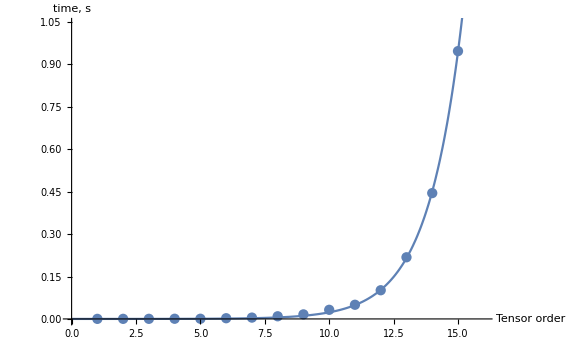

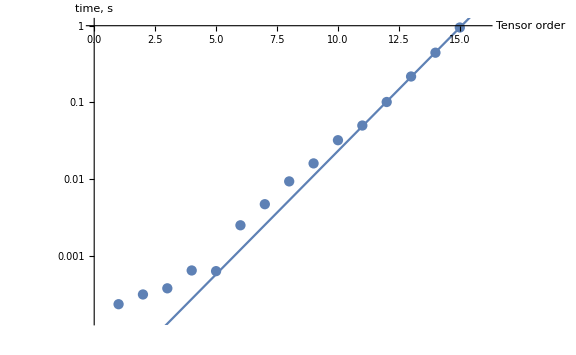

```mathematica
Table[Timing[ITensor[dummyArray[i]]][[1]],{i,1,15}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

C tensor.

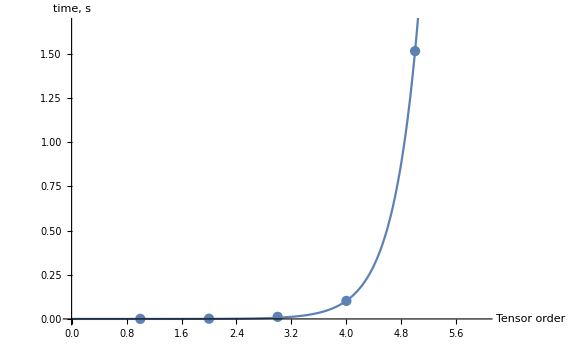

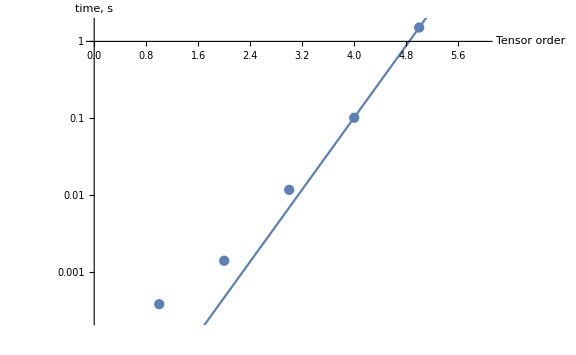

```mathematica
Table[Timing[CTensor[dummyArray[i]]][[1]],{i,1,5}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

CIII tensor.

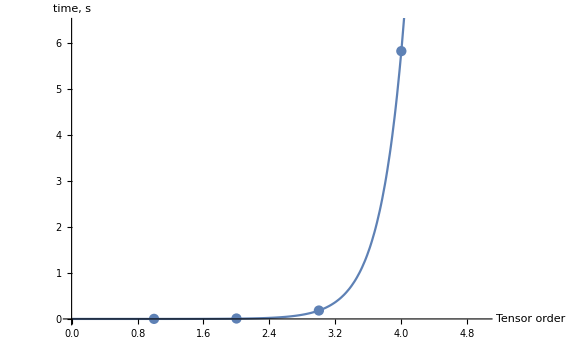

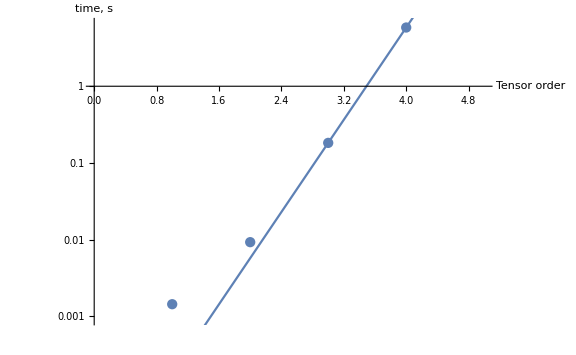

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[i]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton vertex.

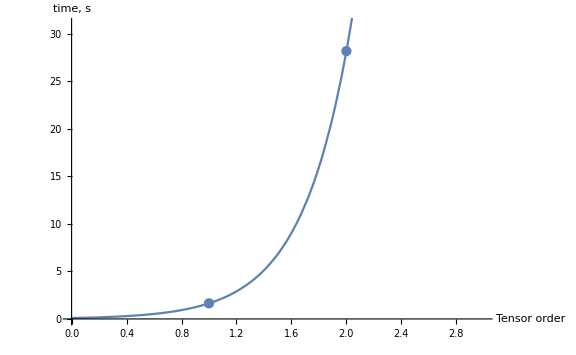

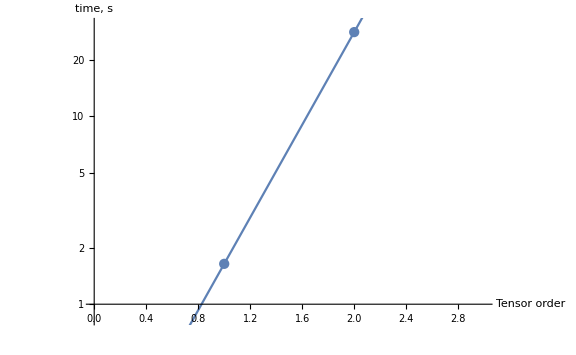

```mathematica
Table[Timing[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[i]]]][[1]],{i,3,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-scalar vertex.

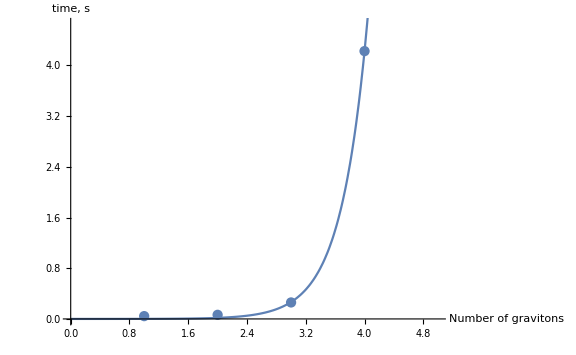

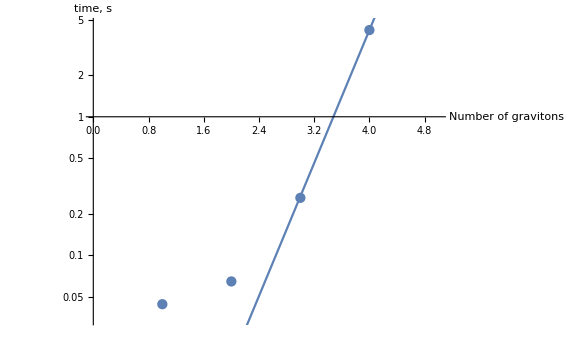

```mathematica
Table[Timing[GravitonScalarVertex[Join[dummyArray[i],{p1,p2}]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-vector vertex.

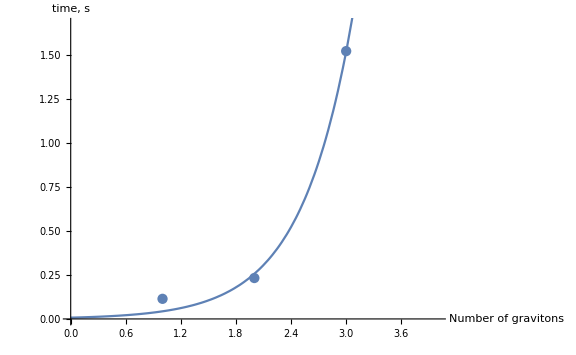

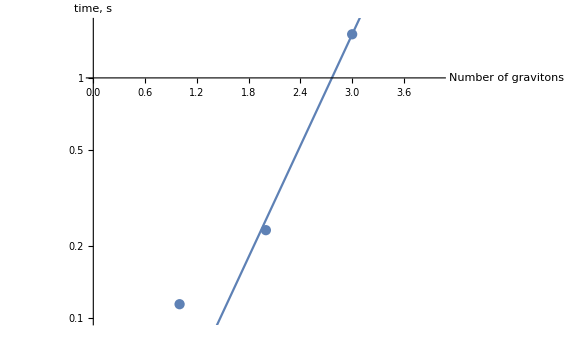

```mathematica
Table[Timing[GravitonVectorVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-fermion vertex.

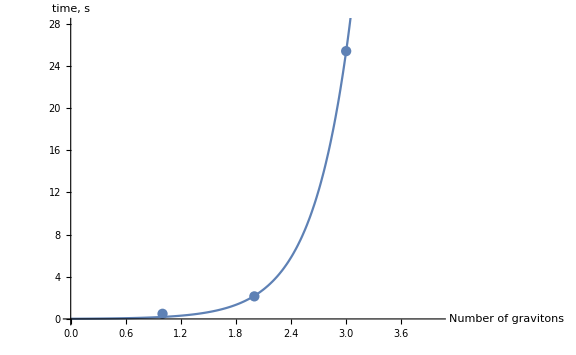

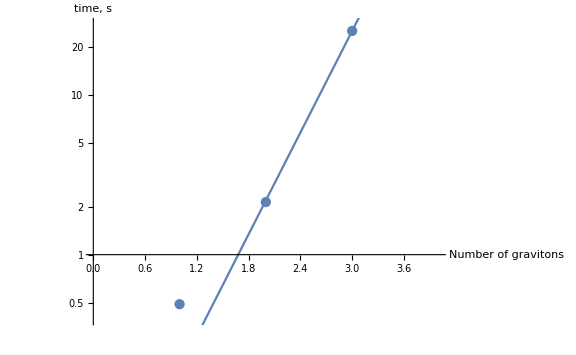

```mathematica
Table[Timing[GravitonFermionVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

# Export procedures.

## Procedures that perform export of interaction vertices.

This command set the working directory to be the directory where this file is placed.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/latosh/Borealis/Science/Wolfram_Packages/FeynGrav/Libs

Export of graviton vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVertex[order_] := Module[{cursor}, 
Print["Export of graviton vertices is initiated."];
For[cursor=3,cursor≤order+2,cursor++,
Evaluate[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[cursor]]]]>>"GravitonVertex_"<>ToString[cursor-2];
Print["Done for order "<>ToString[cursor-2]];
]
]
```

Export of graviton-scalar vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonScalarVertex[order_]:=Module[{cursor},
Print["Export of graviton-scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonScalarVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonMassiveScalarVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
]
```

Export of graviton-vector vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVectorVertex[order_]:=Module[{cursor},
	Print["Export of graviton-Vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}]]]>>"GravitonVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

Export of graviton-fermion vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonFermionVertex[order_]:=Module[{cursor},
	Print["Export of graviton-fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonFermionVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-massive fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveFermionVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

## The actual export. Do not run without a necessity!

The following module runs the export procedure. The export is performed up to the order 𝒪(κ^order).

```mathematica
Module[{order},
order =3;
exportGravitonVertex[order];
exportGravitonScalarVertex[order];
exportGravitonVectorVertex[order];
exportGravitonFermionVertex[order];
]
```

Export of graviton vertices is initiated.

Done for order 1

Done for order 2

Done for order 3

Export of graviton-scalar vertices is initiated.

Done for order 1

Done for order 2

Done for order 3

Export of graviton-Vector vertices is initiated.

Done for order 1

Done for order 2

Done for order 3

Export of graviton-fermion vertices is initiated.

Done for order 1

Done for order 2

Done for order 3